# Main model execution document

```mathematica
SetDirectory[NotebookDirectory[]]
ClearAll[t]
```

/home/eric/git/MCMICM2017/MMAmodel

## Document stocks + stuff with initial conditions

[[SOURCE]] -> lake1inflow -> lake1 -> lake1outflow -> [[SINK]]

```mathematica
initialConds={lake1Vol[0]==1000(*,lake1inflow[t_/;t≤0]==10*)};
behaviors={lake1Vol'[t]==lake1inflow[t]-lake1outflow[t]};
```

## Define lake properties

These convert volume in m^3 into height in meters

```mathematica
lakeEqns={lake1Height[t]==lake1Vol[t]/100};
```

## Define source inflow

```mathematica
inflows={lake1inflow[t]==10+3Sin[t*2 Pi / 365]};
```

## Define dam policies

```mathematica
damPolicy={lake1outflow[t]==lake1Height[t]};
```

## Run simulation

```mathematica
sol=NDSolveValue[{initialConds,behaviors,lakeEqns,inflows,damPolicy},lake1Height[t],{t,365,365*2}]
```

InterpolatingFunction[{{365., 730.}}, <>][t]

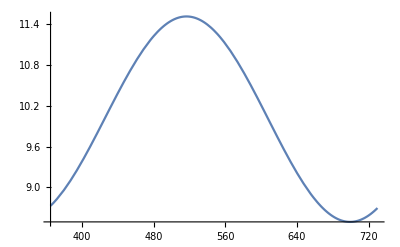

```mathematica
Plot[sol,{t,365,365*2}]
```